# QMeSTools Showcase

## Load Package

```mathematica
(* Load the installed version of the package *)
Needs["QMeSderivation`"]
```

## Define the theory (a QCD truncation)

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fieldsQCD=<|
"bosonic"-> {
σ[p],(*sigma meson*)
Π[p,{a}],(*pions*)
 A[p,{v, c}](*gluon*)
},
 "fermionic"->{
{sb[p,{d,c}],s[p,{d,c}]},(*strange quark*)
{qb[p,{d,c,f}],q[p,{d,c,f}]},(*light quarks*)
{cb[p,{c}],c[p,{c}]}(*ghosts*)
}
|>;

TruncationQCD = {
{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRGQCD= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsQCD,
"Truncation"->TruncationQCD
|>;
```

## FRG Equations: Four-Quark vertex

### Derive flow equation of four-quark vertex

```mathematica
DerivativeListqbqqbq= {qb[p,{d4,c4,f4}],q[-p,{d3,c3,f3}],qb[p,{d2,c2,f2}],q[-p,{d1,c1,f1}]};
Diagramsqbqqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListqbqqbq,"OutputLevel"->"SuperindexDiagrams"];
Diagramsqbqqbq//Length
```

400

### Reduce the number of diagrams by using the symmetries of the tensor structure and the t-channel configuration

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,3},Plus},
{{2,4},Plus},
{{1,3},{2,4},Plus}
};
DiagramsqbqqbqReduced=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,DerivativeListqbqqbq,symmetries];
DiagramsqbqqbqReduced//Length
```

61

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is the corresponding QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

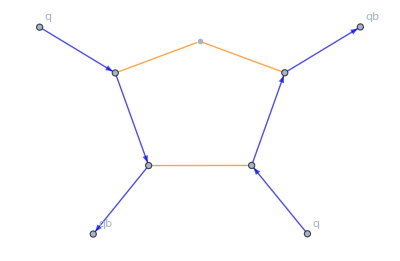
{4,-Graphics-}

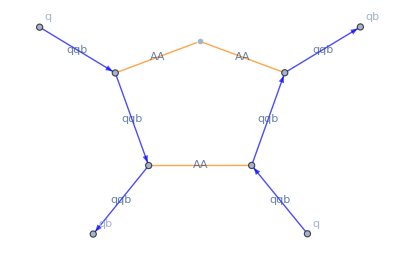
{4,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->True
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

PlotSuperindexDiagram[diagrams, setup, options]

Plot a set of superindex diagrams. The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup.
The diagrams have to be superindex diagrams.

The options for the function PlotSuperindexDiagrams are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

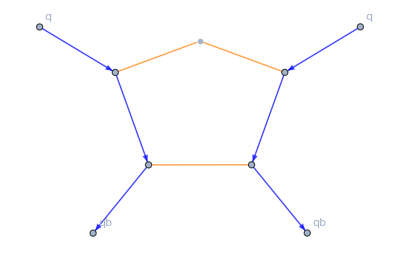
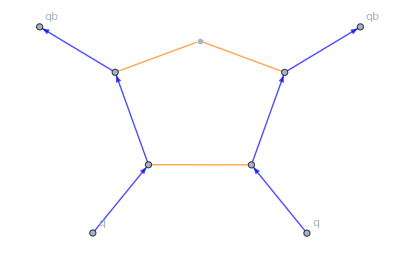
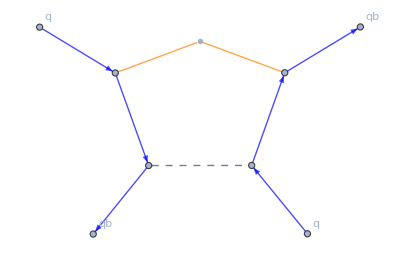
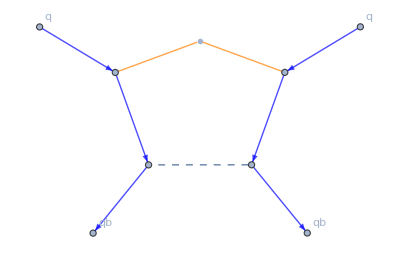
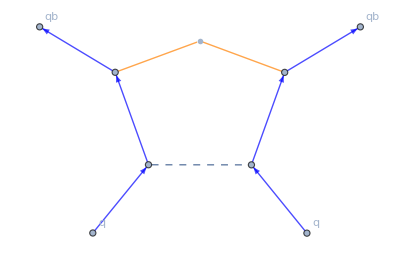
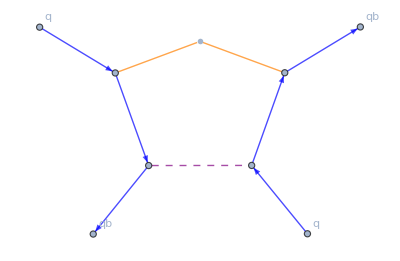
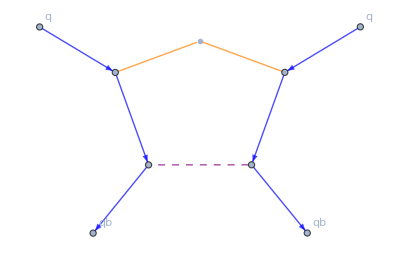
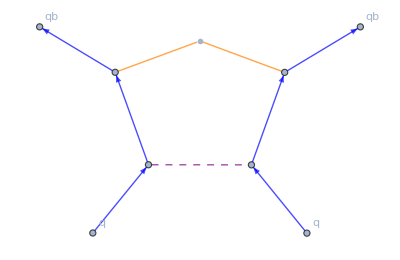
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsqbqqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsqbqqbqFull=SuperindexToFullDiagrams[DiagramsqbqqbqReduced,SetupfRGQCD,DerivativeListqbqqbq];
RerouteFermionicMomenta[DiagramsqbqqbqFull,SetupfRGQCD,DerivativeListqbqqbq]
```

{{4 GAA[{-q,v$33700,c$33700,q,v$33658,c$33658}] GAA[{q,v$33662,c$33662,-q,v$33655,c$33655}] GAA[{q,v$33684,c$33684,-q,v$33678,c$33678}] Gqqb[{-p-q,d$33669,c$33669,f$33669,p+q,d$33674,c$33674,f$33674}] Gqqb[{-p-q,d$33691,c$33691,f$33691,p+q,d$33696,c$33696,f$33696}] RdotAA[{-q,v$33655,c$33655,q,v$33658,c$33658}] ΓAqbq[{-q,v$33678,c$33678,p+q,d$33674,c$33674,f$33674,-p,d3,c3,f3}] ΓAqbq[{-q,v$33700,c$33700,p+q,d$33696,c$33696,f$33696,-p,d1,c1,f1}] ΓAqbq[{q,v$33662,c$33662,p,d4,c4,f4,-p-q,d$33669,c$33669,f$33669}] ΓAqbq[{q,v$33684,c$33684,p,d2,c2,f2,-p-q,d$33691,c$33691,f$33691}]},{2 GAA[{-q,v$33803,c$33803,q,v$33761,c$33761}] GAA[{q,v$33765,c$33765,-q,v$33758,c$33758}] GAA[{q,v$33787,c$33787,-q,v$33781,c$33781}] Gqqb[{-p-q,d$33794,c$33794,f$33794,p+q,d$33799,c$33799,f$33799}] Gqqb[{-p+q,d$33776,c$33776,f$33776,p-q,d$33771,c$33771,f$33771}] RdotAA[{-q,v$33758,c$33758,q,v$33761,c$33761}] ΓAqbq[{-q,v$33781,c$33781,p,d4,c4,f4,-p+q,d$33776,c$33776,f$33776}] ΓAqbq[{-q,v$33803,c$33803,p+q,d$33799,c$33799,f$33799,-p,d1,c1,f1}] ΓAqbq[{q,v$33765,c$33765,p-q,d$33771,c$33771,f$33771,-p,d3,c3,f3}] ΓAqbq[{q,v$33787,c$33787,p,d2,c2,f2,-p-q,d$33794,c$33794,f$33794}]},{-2 GAA[{-q,v$33879,c$33879,q,v$33886,c$33886}] GAA[{-q,v$33901,c$33901,q,v$33859,c$33859}] GAA[{q,v$33863,c$33863,-q,v$33856,c$33856}] Gqqb[{-p-q,d$33870,c$33870,f$33870,p+q,d$33875,c$33875,f$33875}] Gqqb[{-p+q,d$33896,c$33896,f$33896,p-q,d$33891,c$33891,f$33891}] RdotAA[{-q,v$33856,c$33856,q,v$33859,c$33859}] ΓAqbq[{-q,v$33879,c$33879,p+q,d$33875,c$33875,f$33875,-p,d3,c3,f3}] ΓAqbq[{-q,v$33901,c$33901,p,d4,c4,f4,-p+q,d$33896,c$33896,f$33896}] ΓAqbq[{q,v$33863,c$33863,p,d2,c2,f2,-p-q,d$33870,c$33870,f$33870}] ΓAqbq[{q,v$33886,c$33886,p-q,d$33891,c$33891,f$33891,-p,d1,c1,f1}]},{4 GAA[{-q,v$33999,c$33999,q,v$33957,c$33957}] GAA[{q,v$33961,c$33961,-q,v$33954,c$33954}] Gqqb[{-p-q,d$33968,c$33968,f$33968,p+q,d$33973,c$33973,f$33973}] Gqqb[{-p-q,d$33990,c$33990,f$33990,p+q,d$33995,c$33995,f$33995}] GΠΠ[{q,a$33983,-q,a$33977}] RdotAA[{-q,v$33954,c$33954,q,v$33957,c$33957}] ΓAqbq[{-q,v$33999,c$33999,p+q,d$33995,c$33995,f$33995,-p,d1,c1,f1}] ΓAqbq[{q,v$33961,c$33961,p,d4,c4,f4,-p-q,d$33968,c$33968,f$33968}] ΓΠqbq[{-q,a$33977,p+q,d$33973,c$33973,f$33973,-p,d3,c3,f3}] ΓΠqbq[{q,a$33983,p,d2,c2,f2,-p-q,d$33990,c$33990,f$33990}]},{2 GAA[{-q,v$34097,c$34097,q,v$34055,c$34055}] GAA[{q,v$34059,c$34059,-q,v$34052,c$34052}] Gqqb[{-p-q,d$34088,c$34088,f$34088,p+q,d$34093,c$34093,f$34093}] Gqqb[{-p+q,d$34070,c$34070,f$34070,p-q,d$34065,c$34065,f$34065}] GΠΠ[{q,a$34081,-q,a$34075}] RdotAA[{-q,v$34052,c$34052,q,v$34055,c$34055}] ΓAqbq[{-q,v$34097,c$34097,p+q,d$34093,c$34093,f$34093,-p,d1,c1,f1}] ΓAqbq[{q,v$34059,c$34059,p-q,d$34065,c$34065,f$34065,-p,d3,c3,f3}] ΓΠqbq[{-q,a$34075,p,d4,c4,f4,-p+q,d$34070,c$34070,f$34070}] ΓΠqbq[{q,a$34081,p,d2,c2,f2,-p-q,d$34088,c$34088,f$34088}]},{-2 GAA[{-q,v$34195,c$34195,q,v$34153,c$34153}] GAA[{q,v$34157,c$34157,-q,v$34150,c$34150}] Gqqb[{-p-q,d$34164,c$34164,f$34164,p+q,d$34169,c$34169,f$34169}] Gqqb[{-p+q,d$34190,c$34190,f$34190,p-q,d$34185,c$34185,f$34185}] GΠΠ[{-q,a$34173,q,a$34180}] RdotAA[{-q,v$34150,c$34150,q,v$34153,c$34153}] ΓAqbq[{-q,v$34195,c$34195,p,d4,c4,f4,-p+q,d$34190,c$34190,f$34190}] ΓAqbq[{q,v$34157,c$34157,p,d2,c2,f2,-p-q,d$34164,c$34164,f$34164}] ΓΠqbq[{-q,a$34173,p+q,d$34169,c$34169,f$34169,-p,d3,c3,f3}] ΓΠqbq[{q,a$34180,p-q,d$34185,c$34185,f$34185,-p,d1,c1,f1}]},{4 GAA[{-q,v$34291,c$34291,q,v$34251,c$34251}] GAA[{q,v$34255,c$34255,-q,v$34248,c$34248}] Gqqb[{-p-q,d$34262,c$34262,f$34262,p+q,d$34267,c$34267,f$34267}] Gqqb[{-p-q,d$34282,c$34282,f$34282,p+q,d$34287,c$34287,f$34287}] Gσσ[{q,-q}] RdotAA[{-q,v$34248,c$34248,q,v$34251,c$34251}] ΓAqbq[{-q,v$34291,c$34291,p+q,d$34287,c$34287,f$34287,-p,d1,c1,f1}] ΓAqbq[{q,v$34255,c$34255,p,d4,c4,f4,-p-q,d$34262,c$34262,f$34262}] Γσqbq[{-q,p+q,d$34267,c$34267,f$34267,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$34282,c$34282,f$34282}]},{2 GAA[{-q,v$34387,c$34387,q,v$34347,c$34347}] GAA[{q,v$34351,c$34351,-q,v$34344,c$34344}] Gqqb[{-p-q,d$34378,c$34378,f$34378,p+q,d$34383,c$34383,f$34383}] Gqqb[{-p+q,d$34362,c$34362,f$34362,p-q,d$34357,c$34357,f$34357}] Gσσ[{q,-q}] RdotAA[{-q,v$34344,c$34344,q,v$34347,c$34347}] ΓAqbq[{-q,v$34387,c$34387,p+q,d$34383,c$34383,f$34383,-p,d1,c1,f1}] ΓAqbq[{q,v$34351,c$34351,p-q,d$34357,c$34357,f$34357,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$34362,c$34362,f$34362}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$34378,c$34378,f$34378}]},{-2 GAA[{-q,v$34483,c$34483,q,v$34443,c$34443}] GAA[{q,v$34447,c$34447,-q,v$34440,c$34440}] Gqqb[{-p-q,d$34454,c$34454,f$34454,p+q,d$34459,c$34459,f$34459}] Gqqb[{-p+q,d$34478,c$34478,f$34478,p-q,d$34473,c$34473,f$34473}] Gσσ[{-q,q}] RdotAA[{-q,v$34440,c$34440,q,v$34443,c$34443}] ΓAqbq[{-q,v$34483,c$34483,p,d4,c4,f4,-p+q,d$34478,c$34478,f$34478}] ΓAqbq[{q,v$34447,c$34447,p,d2,c2,f2,-p-q,d$34454,c$34454,f$34454}] Γσqbq[{-q,p+q,d$34459,c$34459,f$34459,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$34473,c$34473,f$34473,-p,d1,c1,f1}]},{-4 GAA[{-q,v$34570,c$34570,q,v$34577,c$34577}] GAA[{q,v$34554,c$34554,-q,v$34548,c$34548}] Gqqb[{-p+q,d$34539,c$34539,f$34539,p-q,d$34582,c$34582,f$34582}] Gqqb[{-p+q,d$34543,c$34543,f$34543,p-q,d$34536,c$34536,f$34536}] Gqqb[{-p+q,d$34565,c$34565,f$34565,p-q,d$34560,c$34560,f$34560}] Rdotqbq[{p-q,d$34536,c$34536,f$34536,-p+q,d$34539,c$34539,f$34539}] ΓAqbq[{-q,v$34548,c$34548,p,d4,c4,f4,-p+q,d$34543,c$34543,f$34543}] ΓAqbq[{-q,v$34570,c$34570,p,d2,c2,f2,-p+q,d$34565,c$34565,f$34565}] ΓAqbq[{q,v$34554,c$34554,p-q,d$34560,c$34560,f$34560,-p,d3,c3,f3}] ΓAqbq[{q,v$34577,c$34577,p-q,d$34582,c$34582,f$34582,-p,d1,c1,f1}]},{-4 GAA[{-q,v$34668,c$34668,q,v$34675,c$34675}] GAA[{q,v$34652,c$34652,-q,v$34646,c$34646}] Gqqb[{-p-q,d$34659,c$34659,f$34659,p+q,d$34664,c$34664,f$34664}] Gqqb[{-p+q,d$34637,c$34637,f$34637,p-q,d$34680,c$34680,f$34680}] Gqqb[{-p+q,d$34641,c$34641,f$34641,p-q,d$34634,c$34634,f$34634}] Rdotqbq[{p-q,d$34634,c$34634,f$34634,-p+q,d$34637,c$34637,f$34637}] ΓAqbq[{-q,v$34646,c$34646,p,d4,c4,f4,-p+q,d$34641,c$34641,f$34641}] ΓAqbq[{-q,v$34668,c$34668,p+q,d$34664,c$34664,f$34664,-p,d3,c3,f3}] ΓAqbq[{q,v$34652,c$34652,p,d2,c2,f2,-p-q,d$34659,c$34659,f$34659}] ΓAqbq[{q,v$34675,c$34675,p-q,d$34680,c$34680,f$34680,-p,d1,c1,f1}]},{-4 GAA[{q,v$34750,c$34750,-q,v$34744,c$34744}] Gqqb[{-p+q,d$34735,c$34735,f$34735,p-q,d$34778,c$34778,f$34778}] Gqqb[{-p+q,d$34739,c$34739,f$34739,p-q,d$34732,c$34732,f$34732}] Gqqb[{-p+q,d$34761,c$34761,f$34761,p-q,d$34756,c$34756,f$34756}] GΠΠ[{-q,a$34766,q,a$34773}] Rdotqbq[{p-q,d$34732,c$34732,f$34732,-p+q,d$34735,c$34735,f$34735}] ΓAqbq[{-q,v$34744,c$34744,p,d4,c4,f4,-p+q,d$34739,c$34739,f$34739}] ΓAqbq[{q,v$34750,c$34750,p-q,d$34756,c$34756,f$34756,-p,d3,c3,f3}] ΓΠqbq[{-q,a$34766,p,d2,c2,f2,-p+q,d$34761,c$34761,f$34761}] ΓΠqbq[{q,a$34773,p-q,d$34778,c$34778,f$34778,-p,d1,c1,f1}]},{-4 GAA[{-q,v$34864,c$34864,q,v$34871,c$34871}] Gqqb[{-p+q,d$34833,c$34833,f$34833,p-q,d$34876,c$34876,f$34876}] Gqqb[{-p+q,d$34837,c$34837,f$34837,p-q,d$34830,c$34830,f$34830}] Gqqb[{-p+q,d$34859,c$34859,f$34859,p-q,d$34854,c$34854,f$34854}] GΠΠ[{q,a$34848,-q,a$34842}] Rdotqbq[{p-q,d$34830,c$34830,f$34830,-p+q,d$34833,c$34833,f$34833}] ΓAqbq[{-q,v$34864,c$34864,p,d2,c2,f2,-p+q,d$34859,c$34859,f$34859}] ΓAqbq[{q,v$34871,c$34871,p-q,d$34876,c$34876,f$34876,-p,d1,c1,f1}] ΓΠqbq[{-q,a$34842,p,d4,c4,f4,-p+q,d$34837,c$34837,f$34837}] ΓΠqbq[{q,a$34848,p-q,d$34854,c$34854,f$34854,-p,d3,c3,f3}]},{-4 GAA[{q,v$34946,c$34946,-q,v$34940,c$34940}] Gqqb[{-p-q,d$34953,c$34953,f$34953,p+q,d$34958,c$34958,f$34958}] Gqqb[{-p+q,d$34931,c$34931,f$34931,p-q,d$34974,c$34974,f$34974}] Gqqb[{-p+q,d$34935,c$34935,f$34935,p-q,d$34928,c$34928,f$34928}] GΠΠ[{-q,a$34962,q,a$34969}] Rdotqbq[{p-q,d$34928,c$34928,f$34928,-p+q,d$34931,c$34931,f$34931}] ΓAqbq[{-q,v$34940,c$34940,p,d4,c4,f4,-p+q,d$34935,c$34935,f$34935}] ΓAqbq[{q,v$34946,c$34946,p,d2,c2,f2,-p-q,d$34953,c$34953,f$34953}] ΓΠqbq[{-q,a$34962,p+q,d$34958,c$34958,f$34958,-p,d3,c3,f3}] ΓΠqbq[{q,a$34969,p-q,d$34974,c$34974,f$34974,-p,d1,c1,f1}]},{-4 GAA[{-q,v$35060,c$35060,q,v$35067,c$35067}] Gqqb[{-p-q,d$35051,c$35051,f$35051,p+q,d$35056,c$35056,f$35056}] Gqqb[{-p+q,d$35029,c$35029,f$35029,p-q,d$35072,c$35072,f$35072}] Gqqb[{-p+q,d$35033,c$35033,f$35033,p-q,d$35026,c$35026,f$35026}] GΠΠ[{q,a$35044,-q,a$35038}] Rdotqbq[{p-q,d$35026,c$35026,f$35026,-p+q,d$35029,c$35029,f$35029}] ΓAqbq[{-q,v$35060,c$35060,p+q,d$35056,c$35056,f$35056,-p,d3,c3,f3}] ΓAqbq[{q,v$35067,c$35067,p-q,d$35072,c$35072,f$35072,-p,d1,c1,f1}] ΓΠqbq[{-q,a$35038,p,d4,c4,f4,-p+q,d$35033,c$35033,f$35033}] ΓΠqbq[{q,a$35044,p,d2,c2,f2,-p-q,d$35051,c$35051,f$35051}]},{-4 GAA[{q,v$35142,c$35142,-q,v$35136,c$35136}] Gqqb[{-p+q,d$35127,c$35127,f$35127,p-q,d$35168,c$35168,f$35168}] Gqqb[{-p+q,d$35131,c$35131,f$35131,p-q,d$35124,c$35124,f$35124}] Gqqb[{-p+q,d$35153,c$35153,f$35153,p-q,d$35148,c$35148,f$35148}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$35124,c$35124,f$35124,-p+q,d$35127,c$35127,f$35127}] ΓAqbq[{-q,v$35136,c$35136,p,d4,c4,f4,-p+q,d$35131,c$35131,f$35131}] ΓAqbq[{q,v$35142,c$35142,p-q,d$35148,c$35148,f$35148,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$35153,c$35153,f$35153}] Γσqbq[{q,p-q,d$35168,c$35168,f$35168,-p,d1,c1,f1}]},{-4 GAA[{-q,v$35252,c$35252,q,v$35259,c$35259}] Gqqb[{-p+q,d$35223,c$35223,f$35223,p-q,d$35264,c$35264,f$35264}] Gqqb[{-p+q,d$35227,c$35227,f$35227,p-q,d$35220,c$35220,f$35220}] Gqqb[{-p+q,d$35247,c$35247,f$35247,p-q,d$35242,c$35242,f$35242}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$35220,c$35220,f$35220,-p+q,d$35223,c$35223,f$35223}] ΓAqbq[{-q,v$35252,c$35252,p,d2,c2,f2,-p+q,d$35247,c$35247,f$35247}] ΓAqbq[{q,v$35259,c$35259,p-q,d$35264,c$35264,f$35264,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35227,c$35227,f$35227}] Γσqbq[{q,p-q,d$35242,c$35242,f$35242,-p,d3,c3,f3}]},{-4 GAA[{q,v$35334,c$35334,-q,v$35328,c$35328}] Gqqb[{-p-q,d$35341,c$35341,f$35341,p+q,d$35346,c$35346,f$35346}] Gqqb[{-p+q,d$35319,c$35319,f$35319,p-q,d$35360,c$35360,f$35360}] Gqqb[{-p+q,d$35323,c$35323,f$35323,p-q,d$35316,c$35316,f$35316}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$35316,c$35316,f$35316,-p+q,d$35319,c$35319,f$35319}] ΓAqbq[{-q,v$35328,c$35328,p,d4,c4,f4,-p+q,d$35323,c$35323,f$35323}] ΓAqbq[{q,v$35334,c$35334,p,d2,c2,f2,-p-q,d$35341,c$35341,f$35341}] Γσqbq[{-q,p+q,d$35346,c$35346,f$35346,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$35360,c$35360,f$35360,-p,d1,c1,f1}]},{-4 GAA[{-q,v$35444,c$35444,q,v$35451,c$35451}] Gqqb[{-p-q,d$35435,c$35435,f$35435,p+q,d$35440,c$35440,f$35440}] Gqqb[{-p+q,d$35415,c$35415,f$35415,p-q,d$35456,c$35456,f$35456}] Gqqb[{-p+q,d$35419,c$35419,f$35419,p-q,d$35412,c$35412,f$35412}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$35412,c$35412,f$35412,-p+q,d$35415,c$35415,f$35415}] ΓAqbq[{-q,v$35444,c$35444,p+q,d$35440,c$35440,f$35440,-p,d3,c3,f3}] ΓAqbq[{q,v$35451,c$35451,p-q,d$35456,c$35456,f$35456,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35419,c$35419,f$35419}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$35435,c$35435,f$35435}]},{-4 Gqqb[{-p+q,d$35511,c$35511,f$35511,p-q,d$35554,c$35554,f$35554}] Gqqb[{-p+q,d$35515,c$35515,f$35515,p-q,d$35508,c$35508,f$35508}] Gqqb[{-p+q,d$35537,c$35537,f$35537,p-q,d$35532,c$35532,f$35532}] GΠΠ[{-q,a$35542,q,a$35549}] GΠΠ[{q,a$35526,-q,a$35520}] Rdotqbq[{p-q,d$35508,c$35508,f$35508,-p+q,d$35511,c$35511,f$35511}] ΓΠqbq[{-q,a$35520,p,d4,c4,f4,-p+q,d$35515,c$35515,f$35515}] ΓΠqbq[{-q,a$35542,p,d2,c2,f2,-p+q,d$35537,c$35537,f$35537}] ΓΠqbq[{q,a$35526,p-q,d$35532,c$35532,f$35532,-p,d3,c3,f3}] ΓΠqbq[{q,a$35549,p-q,d$35554,c$35554,f$35554,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$35631,c$35631,f$35631,p+q,d$35636,c$35636,f$35636}] Gqqb[{-p+q,d$35609,c$35609,f$35609,p-q,d$35652,c$35652,f$35652}] Gqqb[{-p+q,d$35613,c$35613,f$35613,p-q,d$35606,c$35606,f$35606}] GΠΠ[{-q,a$35640,q,a$35647}] GΠΠ[{q,a$35624,-q,a$35618}] Rdotqbq[{p-q,d$35606,c$35606,f$35606,-p+q,d$35609,c$35609,f$35609}] ΓΠqbq[{-q,a$35618,p,d4,c4,f4,-p+q,d$35613,c$35613,f$35613}] ΓΠqbq[{-q,a$35640,p+q,d$35636,c$35636,f$35636,-p,d3,c3,f3}] ΓΠqbq[{q,a$35624,p,d2,c2,f2,-p-q,d$35631,c$35631,f$35631}] ΓΠqbq[{q,a$35647,p-q,d$35652,c$35652,f$35652,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$35707,c$35707,f$35707,p-q,d$35748,c$35748,f$35748}] Gqqb[{-p+q,d$35711,c$35711,f$35711,p-q,d$35704,c$35704,f$35704}] Gqqb[{-p+q,d$35733,c$35733,f$35733,p-q,d$35728,c$35728,f$35728}] GΠΠ[{q,a$35722,-q,a$35716}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$35704,c$35704,f$35704,-p+q,d$35707,c$35707,f$35707}] ΓΠqbq[{-q,a$35716,p,d4,c4,f4,-p+q,d$35711,c$35711,f$35711}] ΓΠqbq[{q,a$35722,p-q,d$35728,c$35728,f$35728,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$35733,c$35733,f$35733}] Γσqbq[{q,p-q,d$35748,c$35748,f$35748,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$35803,c$35803,f$35803,p-q,d$35844,c$35844,f$35844}] Gqqb[{-p+q,d$35807,c$35807,f$35807,p-q,d$35800,c$35800,f$35800}] Gqqb[{-p+q,d$35827,c$35827,f$35827,p-q,d$35822,c$35822,f$35822}] GΠΠ[{-q,a$35832,q,a$35839}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$35800,c$35800,f$35800,-p+q,d$35803,c$35803,f$35803}] ΓΠqbq[{-q,a$35832,p,d2,c2,f2,-p+q,d$35827,c$35827,f$35827}] ΓΠqbq[{q,a$35839,p-q,d$35844,c$35844,f$35844,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35807,c$35807,f$35807}] Γσqbq[{q,p-q,d$35822,c$35822,f$35822,-p,d3,c3,f3}]},{-4 Gqqb[{-p-q,d$35921,c$35921,f$35921,p+q,d$35926,c$35926,f$35926}] Gqqb[{-p+q,d$35899,c$35899,f$35899,p-q,d$35940,c$35940,f$35940}] Gqqb[{-p+q,d$35903,c$35903,f$35903,p-q,d$35896,c$35896,f$35896}] GΠΠ[{q,a$35914,-q,a$35908}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$35896,c$35896,f$35896,-p+q,d$35899,c$35899,f$35899}] ΓΠqbq[{-q,a$35908,p,d4,c4,f4,-p+q,d$35903,c$35903,f$35903}] ΓΠqbq[{q,a$35914,p,d2,c2,f2,-p-q,d$35921,c$35921,f$35921}] Γσqbq[{-q,p+q,d$35926,c$35926,f$35926,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$35940,c$35940,f$35940,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$36015,c$36015,f$36015,p+q,d$36020,c$36020,f$36020}] Gqqb[{-p+q,d$35995,c$35995,f$35995,p-q,d$36036,c$36036,f$36036}] Gqqb[{-p+q,d$35999,c$35999,f$35999,p-q,d$35992,c$35992,f$35992}] GΠΠ[{-q,a$36024,q,a$36031}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$35992,c$35992,f$35992,-p+q,d$35995,c$35995,f$35995}] ΓΠqbq[{-q,a$36024,p+q,d$36020,c$36020,f$36020,-p,d3,c3,f3}] ΓΠqbq[{q,a$36031,p-q,d$36036,c$36036,f$36036,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35999,c$35999,f$35999}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36015,c$36015,f$36015}]},{-4 Gqqb[{-p+q,d$36091,c$36091,f$36091,p-q,d$36130,c$36130,f$36130}] Gqqb[{-p+q,d$36095,c$36095,f$36095,p-q,d$36088,c$36088,f$36088}] Gqqb[{-p+q,d$36115,c$36115,f$36115,p-q,d$36110,c$36110,f$36110}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$36088,c$36088,f$36088,-p+q,d$36091,c$36091,f$36091}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$36115,c$36115,f$36115}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36095,c$36095,f$36095}] Γσqbq[{q,p-q,d$36110,c$36110,f$36110,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$36130,c$36130,f$36130,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$36205,c$36205,f$36205,p+q,d$36210,c$36210,f$36210}] Gqqb[{-p+q,d$36185,c$36185,f$36185,p-q,d$36224,c$36224,f$36224}] Gqqb[{-p+q,d$36189,c$36189,f$36189,p-q,d$36182,c$36182,f$36182}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$36182,c$36182,f$36182,-p+q,d$36185,c$36185,f$36185}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36189,c$36189,f$36189}] Γσqbq[{-q,p+q,d$36210,c$36210,f$36210,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36205,c$36205,f$36205}] Γσqbq[{q,p-q,d$36224,c$36224,f$36224,-p,d1,c1,f1}]},{4 GAA[{q,v$36305,c$36305,-q,v$36299,c$36299}] Gqqb[{-p-q,d$36290,c$36290,f$36290,p+q,d$36295,c$36295,f$36295}] Gqqb[{-p-q,d$36312,c$36312,f$36312,p+q,d$36317,c$36317,f$36317}] GΠΠ[{-q,a$36321,q,a$36279}] GΠΠ[{q,a$36283,-q,a$36276}] RdotΠΠ[{-q,a$36276,q,a$36279}] ΓAqbq[{-q,v$36299,c$36299,p+q,d$36295,c$36295,f$36295,-p,d3,c3,f3}] ΓAqbq[{q,v$36305,c$36305,p,d2,c2,f2,-p-q,d$36312,c$36312,f$36312}] ΓΠqbq[{-q,a$36321,p+q,d$36317,c$36317,f$36317,-p,d1,c1,f1}] ΓΠqbq[{q,a$36283,p,d4,c4,f4,-p-q,d$36290,c$36290,f$36290}]},{2 GAA[{q,v$36403,c$36403,-q,v$36397,c$36397}] Gqqb[{-p-q,d$36410,c$36410,f$36410,p+q,d$36415,c$36415,f$36415}] Gqqb[{-p+q,d$36392,c$36392,f$36392,p-q,d$36387,c$36387,f$36387}] GΠΠ[{-q,a$36419,q,a$36377}] GΠΠ[{q,a$36381,-q,a$36374}] RdotΠΠ[{-q,a$36374,q,a$36377}] ΓAqbq[{-q,v$36397,c$36397,p,d4,c4,f4,-p+q,d$36392,c$36392,f$36392}] ΓAqbq[{q,v$36403,c$36403,p,d2,c2,f2,-p-q,d$36410,c$36410,f$36410}] ΓΠqbq[{-q,a$36419,p+q,d$36415,c$36415,f$36415,-p,d1,c1,f1}] ΓΠqbq[{q,a$36381,p-q,d$36387,c$36387,f$36387,-p,d3,c3,f3}]},{-2 GAA[{-q,v$36495,c$36495,q,v$36502,c$36502}] Gqqb[{-p-q,d$36486,c$36486,f$36486,p+q,d$36491,c$36491,f$36491}] Gqqb[{-p+q,d$36512,c$36512,f$36512,p-q,d$36507,c$36507,f$36507}] GΠΠ[{-q,a$36517,q,a$36475}] GΠΠ[{q,a$36479,-q,a$36472}] RdotΠΠ[{-q,a$36472,q,a$36475}] ΓAqbq[{-q,v$36495,c$36495,p+q,d$36491,c$36491,f$36491,-p,d3,c3,f3}] ΓAqbq[{q,v$36502,c$36502,p-q,d$36507,c$36507,f$36507,-p,d1,c1,f1}] ΓΠqbq[{-q,a$36517,p,d4,c4,f4,-p+q,d$36512,c$36512,f$36512}] ΓΠqbq[{q,a$36479,p,d2,c2,f2,-p-q,d$36486,c$36486,f$36486}]},{4 Gqqb[{-p-q,d$36584,c$36584,f$36584,p+q,d$36589,c$36589,f$36589}] Gqqb[{-p-q,d$36606,c$36606,f$36606,p+q,d$36611,c$36611,f$36611}] GΠΠ[{-q,a$36615,q,a$36573}] GΠΠ[{q,a$36577,-q,a$36570}] GΠΠ[{q,a$36599,-q,a$36593}] RdotΠΠ[{-q,a$36570,q,a$36573}] ΓΠqbq[{-q,a$36593,p+q,d$36589,c$36589,f$36589,-p,d3,c3,f3}] ΓΠqbq[{-q,a$36615,p+q,d$36611,c$36611,f$36611,-p,d1,c1,f1}] ΓΠqbq[{q,a$36577,p,d4,c4,f4,-p-q,d$36584,c$36584,f$36584}] ΓΠqbq[{q,a$36599,p,d2,c2,f2,-p-q,d$36606,c$36606,f$36606}]},{2 Gqqb[{-p-q,d$36704,c$36704,f$36704,p+q,d$36709,c$36709,f$36709}] Gqqb[{-p+q,d$36686,c$36686,f$36686,p-q,d$36681,c$36681,f$36681}] GΠΠ[{-q,a$36713,q,a$36671}] GΠΠ[{q,a$36675,-q,a$36668}] GΠΠ[{q,a$36697,-q,a$36691}] RdotΠΠ[{-q,a$36668,q,a$36671}] ΓΠqbq[{-q,a$36691,p,d4,c4,f4,-p+q,d$36686,c$36686,f$36686}] ΓΠqbq[{-q,a$36713,p+q,d$36709,c$36709,f$36709,-p,d1,c1,f1}] ΓΠqbq[{q,a$36675,p-q,d$36681,c$36681,f$36681,-p,d3,c3,f3}] ΓΠqbq[{q,a$36697,p,d2,c2,f2,-p-q,d$36704,c$36704,f$36704}]},{-2 Gqqb[{-p-q,d$36780,c$36780,f$36780,p+q,d$36785,c$36785,f$36785}] Gqqb[{-p+q,d$36806,c$36806,f$36806,p-q,d$36801,c$36801,f$36801}] GΠΠ[{-q,a$36789,q,a$36796}] GΠΠ[{-q,a$36811,q,a$36769}] GΠΠ[{q,a$36773,-q,a$36766}] RdotΠΠ[{-q,a$36766,q,a$36769}] ΓΠqbq[{-q,a$36789,p+q,d$36785,c$36785,f$36785,-p,d3,c3,f3}] ΓΠqbq[{-q,a$36811,p,d4,c4,f4,-p+q,d$36806,c$36806,f$36806}] ΓΠqbq[{q,a$36773,p,d2,c2,f2,-p-q,d$36780,c$36780,f$36780}] ΓΠqbq[{q,a$36796,p-q,d$36801,c$36801,f$36801,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$36878,c$36878,f$36878,p+q,d$36883,c$36883,f$36883}] Gqqb[{-p-q,d$36898,c$36898,f$36898,p+q,d$36903,c$36903,f$36903}] GΠΠ[{-q,a$36907,q,a$36867}] GΠΠ[{q,a$36871,-q,a$36864}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$36864,q,a$36867}] ΓΠqbq[{-q,a$36907,p+q,d$36903,c$36903,f$36903,-p,d1,c1,f1}] ΓΠqbq[{q,a$36871,p,d4,c4,f4,-p-q,d$36878,c$36878,f$36878}] Γσqbq[{-q,p+q,d$36883,c$36883,f$36883,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36898,c$36898,f$36898}]},{2 Gqqb[{-p-q,d$36994,c$36994,f$36994,p+q,d$36999,c$36999,f$36999}] Gqqb[{-p+q,d$36978,c$36978,f$36978,p-q,d$36973,c$36973,f$36973}] GΠΠ[{-q,a$37003,q,a$36963}] GΠΠ[{q,a$36967,-q,a$36960}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$36960,q,a$36963}] ΓΠqbq[{-q,a$37003,p+q,d$36999,c$36999,f$36999,-p,d1,c1,f1}] ΓΠqbq[{q,a$36967,p-q,d$36973,c$36973,f$36973,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36978,c$36978,f$36978}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36994,c$36994,f$36994}]},{-2 Gqqb[{-p-q,d$37070,c$37070,f$37070,p+q,d$37075,c$37075,f$37075}] Gqqb[{-p+q,d$37094,c$37094,f$37094,p-q,d$37089,c$37089,f$37089}] GΠΠ[{-q,a$37099,q,a$37059}] GΠΠ[{q,a$37063,-q,a$37056}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$37056,q,a$37059}] ΓΠqbq[{-q,a$37099,p,d4,c4,f4,-p+q,d$37094,c$37094,f$37094}] ΓΠqbq[{q,a$37063,p,d2,c2,f2,-p-q,d$37070,c$37070,f$37070}] Γσqbq[{-q,p+q,d$37075,c$37075,f$37075,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$37089,c$37089,f$37089,-p,d1,c1,f1}]},{4 GAA[{q,v$37178,c$37178,-q,v$37172,c$37172}] Gqqb[{-p-q,d$37163,c$37163,f$37163,p+q,d$37168,c$37168,f$37168}] Gqqb[{-p-q,d$37185,c$37185,f$37185,p+q,d$37190,c$37190,f$37190}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$37172,c$37172,p+q,d$37168,c$37168,f$37168,-p,d3,c3,f3}] ΓAqbq[{q,v$37178,c$37178,p,d2,c2,f2,-p-q,d$37185,c$37185,f$37185}] Γσqbq[{-q,p+q,d$37190,c$37190,f$37190,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$37163,c$37163,f$37163}]},{2 GAA[{q,v$37272,c$37272,-q,v$37266,c$37266}] Gqqb[{-p-q,d$37279,c$37279,f$37279,p+q,d$37284,c$37284,f$37284}] Gqqb[{-p+q,d$37261,c$37261,f$37261,p-q,d$37256,c$37256,f$37256}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$37266,c$37266,p,d4,c4,f4,-p+q,d$37261,c$37261,f$37261}] ΓAqbq[{q,v$37272,c$37272,p,d2,c2,f2,-p-q,d$37279,c$37279,f$37279}] Γσqbq[{-q,p+q,d$37284,c$37284,f$37284,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$37256,c$37256,f$37256,-p,d3,c3,f3}]},{-2 GAA[{-q,v$37360,c$37360,q,v$37367,c$37367}] Gqqb[{-p-q,d$37351,c$37351,f$37351,p+q,d$37356,c$37356,f$37356}] Gqqb[{-p+q,d$37377,c$37377,f$37377,p-q,d$37372,c$37372,f$37372}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$37360,c$37360,p+q,d$37356,c$37356,f$37356,-p,d3,c3,f3}] ΓAqbq[{q,v$37367,c$37367,p-q,d$37372,c$37372,f$37372,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37377,c$37377,f$37377}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$37351,c$37351,f$37351}]},{4 Gqqb[{-p-q,d$37445,c$37445,f$37445,p+q,d$37450,c$37450,f$37450}] Gqqb[{-p-q,d$37467,c$37467,f$37467,p+q,d$37472,c$37472,f$37472}] GΠΠ[{q,a$37460,-q,a$37454}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$37454,p+q,d$37450,c$37450,f$37450,-p,d3,c3,f3}] ΓΠqbq[{q,a$37460,p,d2,c2,f2,-p-q,d$37467,c$37467,f$37467}] Γσqbq[{-q,p+q,d$37472,c$37472,f$37472,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$37445,c$37445,f$37445}]},{2 Gqqb[{-p-q,d$37561,c$37561,f$37561,p+q,d$37566,c$37566,f$37566}] Gqqb[{-p+q,d$37543,c$37543,f$37543,p-q,d$37538,c$37538,f$37538}] GΠΠ[{q,a$37554,-q,a$37548}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$37548,p,d4,c4,f4,-p+q,d$37543,c$37543,f$37543}] ΓΠqbq[{q,a$37554,p,d2,c2,f2,-p-q,d$37561,c$37561,f$37561}] Γσqbq[{-q,p+q,d$37566,c$37566,f$37566,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$37538,c$37538,f$37538,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$37633,c$37633,f$37633,p+q,d$37638,c$37638,f$37638}] Gqqb[{-p+q,d$37659,c$37659,f$37659,p-q,d$37654,c$37654,f$37654}] GΠΠ[{-q,a$37642,q,a$37649}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$37642,p+q,d$37638,c$37638,f$37638,-p,d3,c3,f3}] ΓΠqbq[{q,a$37649,p-q,d$37654,c$37654,f$37654,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37659,c$37659,f$37659}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$37633,c$37633,f$37633}]},{4 Gqqb[{-p-q,d$37727,c$37727,f$37727,p+q,d$37732,c$37732,f$37732}] Gqqb[{-p-q,d$37747,c$37747,f$37747,p+q,d$37752,c$37752,f$37752}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$37732,c$37732,f$37732,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$37752,c$37752,f$37752,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$37747,c$37747,f$37747}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$37727,c$37727,f$37727}]},{2 Gqqb[{-p-q,d$37839,c$37839,f$37839,p+q,d$37844,c$37844,f$37844}] Gqqb[{-p+q,d$37823,c$37823,f$37823,p-q,d$37818,c$37818,f$37818}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37823,c$37823,f$37823}] Γσqbq[{-q,p+q,d$37844,c$37844,f$37844,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$37839,c$37839,f$37839}] Γσqbq[{q,p-q,d$37818,c$37818,f$37818,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$37911,c$37911,f$37911,p+q,d$37916,c$37916,f$37916}] Gqqb[{-p+q,d$37935,c$37935,f$37935,p-q,d$37930,c$37930,f$37930}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37935,c$37935,f$37935}] Γσqbq[{-q,p+q,d$37916,c$37916,f$37916,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$37911,c$37911,f$37911}] Γσqbq[{q,p-q,d$37930,c$37930,f$37930,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$38018,c$38018,f$38018,p+q,d$38023,c$38023,f$38023}] GΠΠ[{-q,a$38027,q,a$37995}] GΠΠ[{q,a$37999,-q,a$37992}] GΠΠ[{q,a$38011,-q,a$38005}] RdotΠΠ[{-q,a$37992,q,a$37995}] ΓΠqbq[{-q,a$38027,p+q,d$38023,c$38023,f$38023,-p,d1,c1,f1}] ΓΠqbq[{q,a$38011,p,d2,c2,f2,-p-q,d$38018,c$38018,f$38018}] ΓΠΠqbq[{q,a$37999,-q,a$38005,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$38102,c$38102,f$38102,p-q,d$38097,c$38097,f$38097}] GΠΠ[{-q,a$38085,q,a$38092}] GΠΠ[{-q,a$38107,q,a$38075}] GΠΠ[{q,a$38079,-q,a$38072}] RdotΠΠ[{-q,a$38072,q,a$38075}] ΓΠqbq[{-q,a$38107,p,d4,c4,f4,-p+q,d$38102,c$38102,f$38102}] ΓΠqbq[{q,a$38092,p-q,d$38097,c$38097,f$38097,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$38079,-q,a$38085,p,d2,c2,f2,-p,d3,c3,f3}]},{4 Gqqb[{-p-q,d$38176,c$38176,f$38176,p+q,d$38181,c$38181,f$38181}] GΠΠ[{-q,a$38185,q,a$38155}] GΠΠ[{q,a$38159,-q,a$38152}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$38152,q,a$38155}] ΓΠqbq[{-q,a$38185,p+q,d$38181,c$38181,f$38181,-p,d1,c1,f1}] ΓΠσqbq[{q,a$38159,-q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$38176,c$38176,f$38176}]},{-4 Gqqb[{-p+q,d$38258,c$38258,f$38258,p-q,d$38253,c$38253,f$38253}] GΠΠ[{-q,a$38263,q,a$38233}] GΠΠ[{q,a$38237,-q,a$38230}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$38230,q,a$38233}] ΓΠqbq[{-q,a$38263,p,d4,c4,f4,-p+q,d$38258,c$38258,f$38258}] ΓΠσqbq[{q,a$38237,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$38253,c$38253,f$38253,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$38331,c$38331,f$38331,p+q,d$38336,c$38336,f$38336}] GΠΠ[{q,a$38324,-q,a$38317}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$38324,p,d2,c2,f2,-p-q,d$38331,c$38331,f$38331}] ΓΠσqbq[{-q,a$38317,q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$38336,c$38336,f$38336,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$38411,c$38411,f$38411,p-q,d$38406,c$38406,f$38406}] GΠΠ[{-q,a$38393,q,a$38401}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$38401,p-q,d$38406,c$38406,f$38406,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$38393,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$38411,c$38411,f$38411}]},{4 Gqqb[{-p-q,d$38481,c$38481,f$38481,p+q,d$38486,c$38486,f$38486}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$38486,c$38486,f$38486,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$38481,c$38481,f$38481}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$38559,c$38559,f$38559,p-q,d$38554,c$38554,f$38554}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$38559,c$38559,f$38559}] Γσqbq[{q,p-q,d$38554,c$38554,f$38554,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$38611,c$38611,f$38611,p-q,d$38644,c$38644,f$38644}] Gqqb[{-p+q,d$38615,c$38615,f$38615,p-q,d$38608,c$38608,f$38608}] GΠΠ[{-q,a$38632,q,a$38639}] GΠΠ[{q,a$38626,-q,a$38620}] Rdotqbq[{p-q,d$38608,c$38608,f$38608,-p+q,d$38611,c$38611,f$38611}] ΓΠqbq[{-q,a$38620,p,d4,c4,f4,-p+q,d$38615,c$38615,f$38615}] ΓΠqbq[{q,a$38639,p-q,d$38644,c$38644,f$38644,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$38626,-q,a$38632,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$38691,c$38691,f$38691,p-q,d$38722,c$38722,f$38722}] Gqqb[{-p+q,d$38695,c$38695,f$38695,p-q,d$38688,c$38688,f$38688}] GΠΠ[{q,a$38706,-q,a$38700}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$38688,c$38688,f$38688,-p+q,d$38691,c$38691,f$38691}] ΓΠqbq[{-q,a$38700,p,d4,c4,f4,-p+q,d$38695,c$38695,f$38695}] ΓΠσqbq[{q,a$38706,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$38722,c$38722,f$38722,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$38769,c$38769,f$38769,p-q,d$38800,c$38800,f$38800}] Gqqb[{-p+q,d$38773,c$38773,f$38773,p-q,d$38766,c$38766,f$38766}] GΠΠ[{-q,a$38787,q,a$38795}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$38766,c$38766,f$38766,-p+q,d$38769,c$38769,f$38769}] ΓΠqbq[{q,a$38795,p-q,d$38800,c$38800,f$38800,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$38787,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$38773,c$38773,f$38773}]},{-4 Gqqb[{-p+q,d$38847,c$38847,f$38847,p-q,d$38876,c$38876,f$38876}] Gqqb[{-p+q,d$38851,c$38851,f$38851,p-q,d$38844,c$38844,f$38844}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$38844,c$38844,f$38844,-p+q,d$38847,c$38847,f$38847}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$38851,c$38851,f$38851}] Γσqbq[{q,p-q,d$38876,c$38876,f$38876,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$38933,q,a$38940}] GΠΠ[{-q,a$38945,q,a$38923}] GΠΠ[{q,a$38927,-q,a$38920}] RdotΠΠ[{-q,a$38920,q,a$38923}] ΓΠΠqbq[{q,a$38927,-q,a$38933,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠΠqbq[{q,a$38940,-q,a$38945,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 GΠΠ[{-q,a$39004,q,a$38985}] GΠΠ[{q,a$38989,-q,a$38982}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$38982,q,a$38985}] ΓΠσqbq[{-q,a$39004,q,p,d4,c4,f4,-p,d1,c1,f1}] ΓΠσqbq[{q,a$38989,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$39051,q,a$39059}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠσqbq[{-q,a$39051,q,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠσqbq[{q,a$39059,-q,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d1,c1,f1}]}}

## FRG Equations: Three-gluon vertex

### Derive flow equation of three-gluon vertex

```mathematica
DerivativeListAAA= {A[p1,{v1,c1}],A[p2,{v3,c3}],A[p3,{v3,c3}]};
DiagramsAAA=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListAAA,"OutputLevel"->"SuperindexDiagrams"];
DiagramsAAA//Length
```

48

### Reduce the number of diagrams on the symmetric point

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,2},Plus},
{{2,3},Plus},
{{3,1},Plus},
{{1,2,3},Plus},
{{3,2,1},Plus}
};
DiagramsAAAReduced=ReduceIdenticalFlowDiagrams[DiagramsAAA,DerivativeListAAA,symmetries];
DiagramsAAAReduced//Length
```

5

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is the corresponding QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

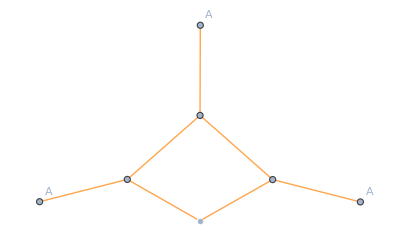
{-3,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsAAAReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

PlotSuperindexDiagram[diagrams, setup, options]

Plot a set of superindex diagrams. The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup.
The diagrams have to be superindex diagrams.

The options for the function PlotSuperindexDiagrams are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

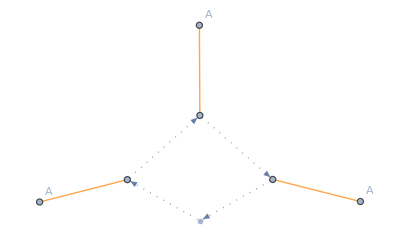
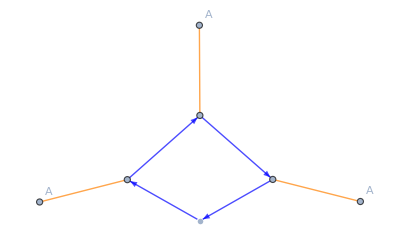
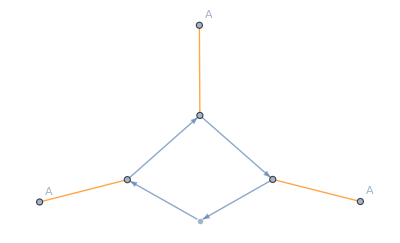
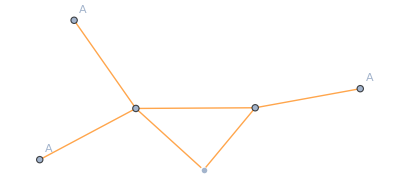
{{-3,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{3,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsAAAReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsAAAFull=SuperindexToFullDiagrams[DiagramsAAAReduced,SetupfRGQCD,DerivativeListAAA];
RerouteFermionicMomenta[DiagramsAAAFull,SetupfRGQCD,DerivativeListAAA]
```

{{-3 GAA[{p3-q,v$45423,c$45423,-p3+q,v$45429,c$45429}] GAA[{-q,v$45434,c$45434,q,v$45402,c$45402}] GAA[{q,v$45406,c$45406,-q,v$45399,c$45399}] GAA[{-p2-p3+q,v$45417,c$45417,p2+p3-q,v$45412,c$45412}] RdotAA[{-q,v$45399,c$45399,q,v$45402,c$45402}] ΓAAA[{q,v$45406,c$45406,p2+p3-q,v$45412,c$45412,-p2-p3,v1,c1}] ΓAAA[{-p3+q,v$45429,c$45429,-q,v$45434,c$45434,p3,v3,c3}] ΓAAA[{-p2-p3+q,v$45417,c$45417,p3-q,v$45423,c$45423,p2,v3,c3}]},{-6 Gccb[{qf,c$45481,-qf,c$45486}] Gccb[{qf,c$45514,-qf,c$45478}] Gccb[{p3+qf,c$45503,-p3-qf,c$45508}] Gccb[{p2+p3+qf,c$45492,-p2-p3-qf,c$45497}] Rdotcbc[{-qf,c$45478,qf,c$45481}] ΓAcbc[{p2,v3,c3,-p2-p3-qf,c$45497,p3+qf,c$45503}] ΓAcbc[{-p2-p3,v1,c1,-qf,c$45486,p2+p3+qf,c$45492}] ΓAcbc[{p3,v3,c3,-p3-qf,c$45508,qf,c$45514}]},{-6 Gqqb[{qf,d$45560,c$45560,f$45560,-qf,d$45565,c$45565,f$45565}] Gqqb[{qf,d$45593,c$45593,f$45593,-qf,d$45557,c$45557,f$45557}] Gqqb[{p3+qf,d$45582,c$45582,f$45582,-p3-qf,d$45587,c$45587,f$45587}] Gqqb[{p2+p3+qf,d$45571,c$45571,f$45571,-p2-p3-qf,d$45576,c$45576,f$45576}] Rdotqbq[{-qf,d$45557,c$45557,f$45557,qf,d$45560,c$45560,f$45560}] ΓAqbq[{p2,v3,c3,-p2-p3-qf,d$45576,c$45576,f$45576,p3+qf,d$45582,c$45582,f$45582}] ΓAqbq[{-p2-p3,v1,c1,-qf,d$45565,c$45565,f$45565,p2+p3+qf,d$45571,c$45571,f$45571}] ΓAqbq[{p3,v3,c3,-p3-qf,d$45587,c$45587,f$45587,qf,d$45593,c$45593,f$45593}]},{-6 Gssb[{qf,d$45639,c$45639,-qf,d$45644,c$45644}] Gssb[{qf,d$45672,c$45672,-qf,d$45636,c$45636}] Gssb[{p3+qf,d$45661,c$45661,-p3-qf,d$45666,c$45666}] Gssb[{p2+p3+qf,d$45650,c$45650,-p2-p3-qf,d$45655,c$45655}] Rdotsbs[{-qf,d$45636,c$45636,qf,d$45639,c$45639}] ΓAsbs[{p2,v3,c3,-p2-p3-qf,d$45655,c$45655,p3+qf,d$45661,c$45661}] ΓAsbs[{-p2-p3,v1,c1,-qf,d$45644,c$45644,p2+p3+qf,d$45650,c$45650}] ΓAsbs[{p3,v3,c3,-p3-qf,d$45666,c$45666,qf,d$45672,c$45672}]},{3 GAA[{p3-q,v$45728,c$45728,-p3+q,v$45735,c$45735}] GAA[{-q,v$45740,c$45740,q,v$45718,c$45718}] GAA[{q,v$45722,c$45722,-q,v$45715,c$45715}] RdotAA[{-q,v$45715,c$45715,q,v$45718,c$45718}] ΓAAA[{-p3+q,v$45735,c$45735,-q,v$45740,c$45740,p3,v3,c3}] ΓAAAA[{q,v$45722,c$45722,p3-q,v$45728,c$45728,-p2-p3,v1,c1,p2,v3,c3}]}}